```mathematica
(*** birth-immigration-death analysis for minirhizotron data ***)
```

```mathematica
SetDirectory["~/Dropbox/Documents/2020_Projects/BIFoR_draft/Datasets/Curate1/"]
workingdir="";
```

/home/iain/Dropbox/Documents/2020_Projects/BIFoR_draft/Datasets/Curate1

```mathematica
(*** generating function for BID process ***)
```

```mathematica
G = ((ν-λ)/(λ Exp[(λ-ν)t](z-1)-λ z + ν))^(α/λ) * ((ν Exp[(λ-ν)t](z-1) - λ z + ν)/(λ Exp[(λ-ν)t](z-1) - λ z + ν))^m0
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) ((-z λ+ν+ⅇ^(t (λ-ν)) (-1+z) ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^m0

```mathematica
(*** expressions for mean and variance ***)
```

```mathematica
Simplify[D[G, z]/.z->1]
```

((-1+ⅇ^(t (λ-ν))) α+ⅇ^(t (λ-ν)) m0 (λ-ν))/(λ-ν)

```mathematica
Simplify[(D[G,{z,2}]+D[G, z]-(D[G, z]^2))/.z->1]
```

((-1+ⅇ^(t (λ-ν))) (-α ν+ⅇ^(t (λ-ν)) (α λ+m0 (λ^2-ν^2))))/(λ-ν)^2

```mathematica
(*** get data ***)
```

```mathematica
l = ReadList[workingdir<>"roots-bid-data.txt", String];
```

```mathematica
lt = Table[ToExpression[StringSplit[l[[i]]]], {i, 1, Length[l]}];
```

```mathematica
controlt = Select[lt, #[[1]]===Control&];
eco2t = Select[lt, #[[1]]===eCO2&];
```

```mathematica
control = eco2 = {};
For[i=1,i≤Length[controlt],i++,
If[controlt[[i]][[2]]<175, AppendTo[control, {controlt[[i]][[1]], controlt[[i]][[2]], Log[controlt[[i]][[3]]], Log[controlt[[i]][[4]]]}];
];
];
For[i=1,i≤Length[eco2t],i++,
If[eco2t[[i]][[2]]<175, AppendTo[eco2, {eco2t[[i]][[1]], eco2t[[i]][[2]], Log[eco2t[[i]][[3]]], Log[eco2t[[i]][[4]]]}];
];
];
```

```mathematica
control = eco2 = {};
For[i=1,i≤Length[controlt],i++,
If[controlt[[i]][[2]]< 300, AppendTo[control, {controlt[[i]][[1]], controlt[[i]][[2]], controlt[[i]][[3]], controlt[[i]][[4]]}];
];
];
For[i=1,i≤Length[eco2t],i++,
If[eco2t[[i]][[2]]< 300, AppendTo[eco2, {eco2t[[i]][[1]], eco2t[[i]][[2]], eco2t[[i]][[3]], eco2t[[i]][[4]]}];
];
];
```

```mathematica
controlm0 = Mean[Transpose[control][[3]]];
eco2m0 = Mean[Transpose[eco2][[3]]];
bothm0 = Mean[{controlm0, eCO2m0}];
```

```mathematica
(*** functions to report mean and standard deviation. both take time and initial condition as arguments. s.d. function has an additional model parameter: v0, the initial variance, which can also be viewed as the variance due to noisy observations ***)
```

```mathematica
μ[t_, m0_]:= ((-1+ⅇ^(t (λ-ν))) α+ⅇ^(t (λ-ν)) m0 (λ-ν))/(λ-ν)
σ[t_, m0_]:=Sqrt[v0+((-1+ⅇ^(t (λ-ν))) (-α ν+ⅇ^(t (λ-ν)) (α λ+m0 (λ^2-ν^2))))/(λ-ν)^2]
```

```mathematica
controlplotlength = Table[{control[[i]][[2]], control[[i]][[4]]}, {i, 1, Length[control]}];
eco2plotlength = Table[{eco2[[i]][[2]],eco2[[i]][[4]]}, {i, 1, Length[eco2]}];
```

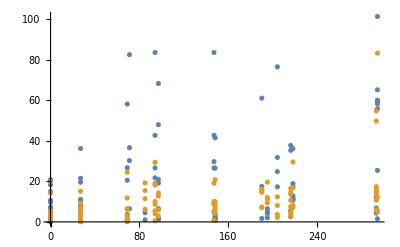

```mathematica
ListPlot[{controlplotlength, eco2plotlength}, PlotRange->All]
```

```mathematica
(*** use these functions and a normality assumption to construct total log likelihoods for the control and eco2 data ***)
```

```mathematica
controllik = Total[Table[LogLikelihood[NormalDistribution[μ[control[[i]][[2]],control[[i]][[3]]], σ[control[[i]][[2]],control[[i]][[3]]]], {control[[i]][[4]]}], {i, 1, Length[control]}]];
```

```mathematica
eco2lik = Total[Table[LogLikelihood[NormalDistribution[μ[eco2[[i]][[2]],eco2[[i]][[3]]], σ[eco2[[i]][[2]],eco2[[i]][[3]]]], {eco2[[i]][[4]]}], {i, 1, Length[eco2]}]];
```

```mathematica
(*** bootstrap the data to get confidence intervals on the parameter values ***)
```

```mathematica
nboot = 100;
```

```mathematica
eco2set = {};
controlset = {};
For[boot=1,boot ≤ nboot, boot++,
bootcontrol = control[[RandomInteger[{1, Length[control]}, Length[control]]]];
booteco2 = eco2[[RandomInteger[{1, Length[eco2]}, Length[eco2]]]];
controllik = Total[Table[LogLikelihood[NormalDistribution[μ[bootcontrol[[i]][[2]],m0], σ[bootcontrol[[i]][[2]],m0]], {bootcontrol[[i]][[4]]}], {i, 1, Length[bootcontrol]}]];
eco2lik = Total[Table[LogLikelihood[NormalDistribution[μ[booteco2[[i]][[2]],m0], σ[booteco2[[i]][[2]],m0]], {booteco2[[i]][[4]]}], {i, 1, Length[booteco2]}]];
AppendTo[controlset, NMaximize[{controllik, λ<ν, λ>0, ν>0, α>0, v0>0, m0>0}, {{λ, 0, 0.19}, {ν, 0, 0.19}, {α, 0, 0.22},{v0, 0,30}, m0}]];
AppendTo[eco2set, NMaximize[{eco2lik, λ<ν, λ>0, ν>0, α>0, v0>0, m0>0}, {{λ, 0, 0.19}, {ν, 0, 0.19}, {α, 0, 0.22},{v0, 0,30}, m0}]];
];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {m0,v0,α,λ,ν} = {6.27532,0.,0.367799,0.23118,0.23502}.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMaximize::nnum: The function value Indeterminate is not a number at {m0,v0,α,λ,ν} = {3.82645,71.8997,0.,0.,0.}.

NMaximize::nnum: The function value Indeterminate is not a number at {m0,v0,α,λ,ν} = {2.81334,52.801,0.000162215,0.,0.}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

```mathematica
Median[(λ-ν)/.Transpose[controlset][[2]]]
Median[(λ-ν)/.Transpose[eco2set][[2]]]
```

-0.0142181

-3.37851×10^-13

```mathematica
(*** bootstrapped statistics and histograms ***)
```

```mathematica
Median[(λ-ν)/.Transpose[controlset][[2]]]
Median[(λ-ν)/.Transpose[eco2set][[2]]]
```

-0.0142181

-3.37851×10^-13

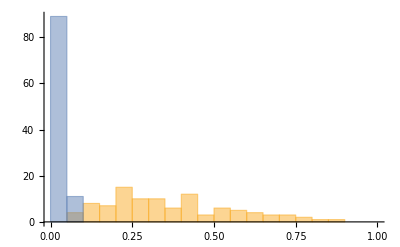

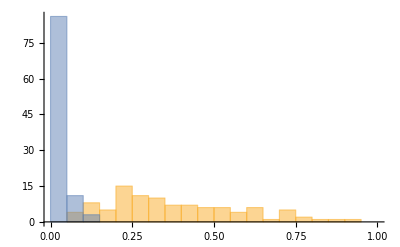

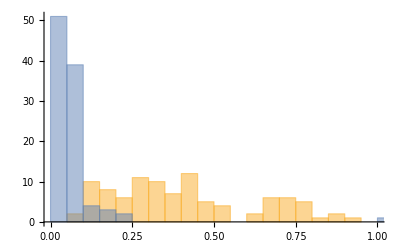

```mathematica
Histogram[{λ/.Transpose[controlset][[2]], λ/.Transpose[eco2set][[2]]}, {0.05},PlotRange->{{0,1},Automatic}]
Histogram[{ν/.Transpose[controlset][[2]], ν/.Transpose[eco2set][[2]]}, {0.05}, PlotRange->{{0,1},Automatic}]
Histogram[{α/.Transpose[controlset][[2]], α/.Transpose[eco2set][[2]]}, {0.05},PlotRange->{{0,1},Automatic}]
```

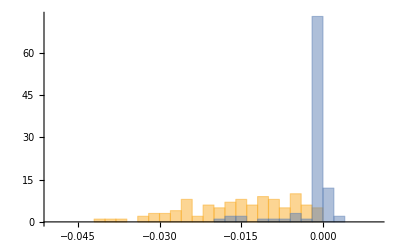

```mathematica
Histogram[{(λ-ν)/.Transpose[controlset][[2]], (λ-ν)/.Transpose[eco2set][[2]]}, {0.002},PlotRange->{{-0.05,0.01},Automatic}]
```

```mathematica
diffsamp = {}; count = 0;
For[i=1,i≤ 10000, i++,
r1 = RandomInteger[{1, Length[controlset]}];
r2 = RandomInteger[{1, Length[eco2set]}];
controlval = (λ-ν)/.controlset[[r1]][[2]];
eco2val = (λ-ν)/.eco2set[[r1]][[2]];
AppendTo[diffsamp, controlval-eco2val];
If[controlval > eco2val, count++];
];
```

```mathematica
N[count/10000]
```

0.0485

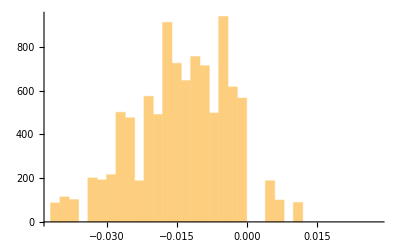

```mathematica
Histogram[diffsamp]
```

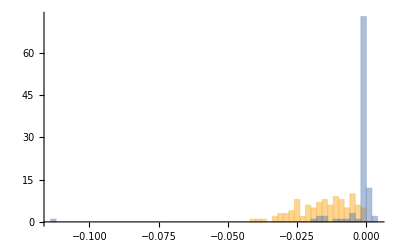

```mathematica
Histogram[{(λ-ν)/.Transpose[controlset][[2]], (λ-ν)/.Transpose[eco2set][[2]]}, {0.002}, PlotRange->All]
```

```mathematica
(*** now do a single maximum likelihood calculation for separate and combined datasets ***)
```

```mathematica
bootcontrol = control;
booteco2 = eco2;
controllik = Total[Table[LogLikelihood[NormalDistribution[μ[bootcontrol[[i]][[2]],m0], σ[bootcontrol[[i]][[2]],m0]], {bootcontrol[[i]][[4]]}], {i, 1, Length[bootcontrol]}]];
eco2lik = Total[Table[LogLikelihood[NormalDistribution[μ[booteco2[[i]][[2]],m0], σ[booteco2[[i]][[2]],m0]], {booteco2[[i]][[4]]}], {i, 1, Length[booteco2]}]];
bothlik = Join[controllik, eco2lik];
mlikcontrol= NMaximize[{controllik, λ>0, ν>0, α>0, v0>0, m0>0}, {{λ, 0, 0.19}, {ν, 0, 0.19}, {α, 0, 0.22},{v0, 0,30}, {m0, 0, 100}}];
mlikeco2= NMaximize[{eco2lik,  λ>0, ν>0, α>0, v0>0, m0>0}, {{λ, 0, 0.19}, {ν, 0, 0.19}, {α, 0, 0.22},{v0, 0,30}, {m0, 0, 100}}];
mlikboth= NMaximize[{bothlik, λ>0, ν>0, α>0, v0>0, m0>0}, {{λ, 0, 0.19}, {ν, 0, 0.19}, {α, 0, 0.22},{v0, 0,30}, {m0, 0, 100}}];
```

```mathematica
(*** examine likelihoods (and max lik parameter values ***)
```

```mathematica
mlikboth
mlikeco2
mlikcontrol
```

{-807.837,{λ→0.204074,ν→0.212141,α→0.185333,v0→46.9299,m0→7.0915}}

{-339.779,{λ→0.0103896,ν→0.00490719,α→5.46902×10^-11,v0→32.0253,m0→4.46516}}

{-417.793,{λ→0.316881,ν→0.329319,α→0.347444,v0→45.5289,m0→9.50284}}

```mathematica
(λ-ν)/.mlikeco2[[2]]
(λ-ν)/.mlikcontrol[[2]]
```

0.00548241

-0.0124376

```mathematica
(*** likelihood ratio test ***)
```

```mathematica
wilkesstat=2*((mlikcontrol[[1]]+mlikeco2[[1]])-mlikboth[[1]] )
```

100.532

```mathematica
1-CDF[ChiSquareDistribution[4],x]/.x->wilkesstat
```

0.

```mathematica
(*** plot mean and s.d. behaviour for max lik parameters for combined dataset ***)
```

```mathematica
bothmean = Table[{t, μ[t, m0]/.mlikboth[[2]]}, {t, 0,300}];
```

```mathematica
bothsd1= Table[{t,( μ[t, m0]+σ[t,m0])/.mlikboth[[2]]}, {t, 0,300}];
bothsd2= Table[{t,( μ[t, m0]-σ[t,m0])/.mlikboth[[2]]}, {t, 0, 300}];
```

```mathematica
bothdata = Join[ Table[{control[[i]][[2]], control[[i]][[4]]}, {i, 1, Length[control]}],  Table[{eco2[[i]][[2]], eco2[[i]][[4]]}, {i, 1, Length[eco2]}]];
```

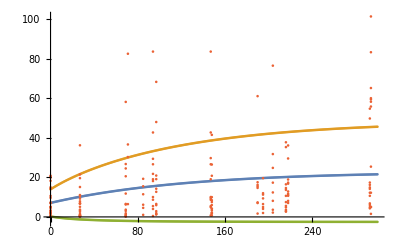

```mathematica
ListPlot[{bothmean, bothsd1, bothsd2, bothdata}]
```

```mathematica
(*** plot mean and s.d. behaviour for max lik parameters for control vs eco2 datasets ***)
```

```mathematica
controlfit = mlikcontrol;
eco2fit = mlikeco2;
```

```mathematica
controlmean = Table[{t, μ[t, m0]/.controlfit[[2]]}, {t, 0, 300}];
eco2mean = Table[{t, μ[t, m0]/.eco2fit[[2]]}, {t, 0, 300}];
```

```mathematica
controlsd1= Table[{t,( μ[t,m0]+σ[t,m0])/.controlfit[[2]]}, {t, 0, 300}];
controlsd2= Table[{t,( μ[t, m0]-σ[t,m0])/.controlfit[[2]]}, {t, 0, 300}];
```

```mathematica
controldata = Table[{control[[i]][[2]], control[[i]][[4]]}, {i, 1, Length[control]}];
```

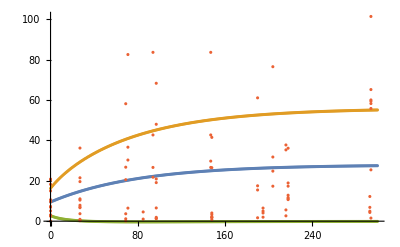

```mathematica
ListPlot[{controlmean, controlsd1, controlsd2, controldata}]
```

```mathematica
eco2sd1= Table[{t,( μ[t, m0]+σ[t,m0])/.eco2fit[[2]]}, {t, 0, 300}];
eco2sd2= Table[{t,( μ[t, m0]-σ[t,m0])/.eco2fit[[2]]}, {t, 0,300}];
```

```mathematica
eco2data = Table[{eco2[[i]][[2]], eco2[[i]][[4]]}, {i, 1, Length[eco2]}];
```

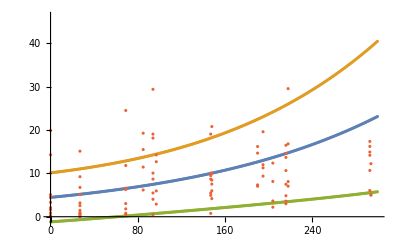

```mathematica
ListPlot[{eco2mean, eco2sd1, eco2sd2, eco2data}]
```

```mathematica
fitset = Table[{bothmean[[i]][[1]], bothmean[[i]][[2]], bothsd1[[i]][[2]], bothsd2[[i]][[2]], controlmean[[i]][[2]], controlsd1[[i]][[2]], controlsd2[[i]][[2]], eco2mean[[i]][[2]], eco2sd1[[i]][[2]], eco2sd2[[i]][[2]]}, {i, 1, Length[bothmean]}];
Export[workingdir<>"fitset.txt", fitset, "Table"]
```

fitset.txt

```mathematica
Export[workingdir<>"bothdata.txt", bothdata, "Table"]
Export[workingdir<>"controldata.txt",controldata, "Table"]
Export[workingdir<>"eco2data.txt", eco2data, "Table"]
```

bothdata.txt

controldata.txt

eco2data.txt

```mathematica
Export[workingdir<>"controlboot.txt", {λ, ν, α, v0, m0}/.Transpose[controlset][[2]], "Table"]
Export[workingdir<>"eco2boot.txt", {λ, ν, α, v0, m0}/.Transpose[eco2set][[2]], "Table"]
```

controlboot.txt

eco2boot.txt

```mathematica
bccontrol = BinCounts[(λ-ν)/.Transpose[controlset][[2]], { -0.05,0.01, 0.002}]
bceco2 = BinCounts[(λ-ν)/.Transpose[eco2set][[2]], { -0.05,0.01, 0.002}]
binhists=Table[{-0.05+0.002*(i-1), N[bccontrol[[i]]/Total[bccontrol]], N[bceco2[[i]]/Total[bceco2]]}, {i, 1, Length[bccontrol]}]
```

{0,0,0,0,1,1,1,0,2,3,3,4,8,2,6,5,7,8,6,9,8,5,10,6,5,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,2,0,1,1,1,3,1,73,12,2,0,0,0}

{{-0.05,0.,0.},{-0.048,0.,0.},{-0.046,0.,0.},{-0.044,0.,0.},{-0.042,0.01,0.},{-0.04,0.01,0.},{-0.038,0.01,0.},{-0.036,0.,0.},{-0.034,0.02,0.},{-0.032,0.03,0.},{-0.03,0.03,0.},{-0.028,0.04,0.},{-0.026,0.08,0.},{-0.024,0.02,0.},{-0.022,0.06,0.},{-0.02,0.05,0.010101},{-0.018,0.07,0.020202},{-0.016,0.08,0.020202},{-0.014,0.06,0.},{-0.012,0.09,0.010101},{-0.01,0.08,0.010101},{-0.008,0.05,0.010101},{-0.006,0.1,0.030303},{-0.004,0.06,0.010101},{-0.002,0.05,0.737374},{0.,0.,0.121212},{0.002,0.,0.020202},{0.004,0.,0.},{0.006,0.,0.},{0.008,0.,0.}}

```mathematica
Export[workingdir<>"binhists.txt", binhists, "Table"]
```

binhists.txt